```mathematica
(*cubic_graph"n".g6 (n=6,8,...,16) stores all cubic graphs of order n, which can be obtained using SageMath (see the file Generate_Cubic_Graphs.ipynb).*)
```

```mathematica
For[n=6,n≤14,n=n+2,
GList=Import[StringJoin["D:\\Cubic_Graphs\\cubic_graph",ToString[n],".g6"]];
NumG=Length[GList];
CharPoly=CharacteristicPolynomial[AdjacencyMatrix[GList[[1]]],x];
L=Table[{CharPoly,k},{k,1,NumG}];
For[i=1,i≤NumG,i++,
A=AdjacencyMatrix[GList[[i]]];
L[[i,1]]=CharacteristicPolynomial[A,x];
];
SL=Sort[L];
CPair={};
For[i=1,i<NumG,i++,
If[SL[[i,1]]==SL[[i+1,1]],CPair=Join[CPair,{{SL[[i,2]],SL[[i+1,2]]}}]];
];
Print["Graph Order:=",n,";","Cospectral Pairs:",CPair];
]
```

Graph Order:=6;Cospectral Pairs:{}

Graph Order:=8;Cospectral Pairs:{}

Graph Order:=10;Cospectral Pairs:{}

Graph Order:=12;Cospectral Pairs:{}

Graph Order:=14;Cospectral Pairs:{{84,471},{208,210},{243,248}}

```mathematica
(* No cospectral pairs among cubic graphs with at most 12 vertices. And there are exactly 3 cospectral pairs among cubic graphs or order 14*)
```

```mathematica
For[i=1,i≤Length[CPair],i++,
G=GList[[CPair[[i,1]]]];
H=GList[[CPair[[i,1]]]];
H=Print[HamiltonianGraphQ[G],HamiltonianGraphQ[H]];
]
```

TrueTrue

TrueTrue

TrueTrue

```mathematica
(*The six graphs in the three cospectral pairs are all Hamiltonian and hence are 3-edge-colorable. We move to the case that n=16*)
```

```mathematica
GList=Import[StringJoin["D:\\Cubic_Graphs\\cubic_graph16.g6"]];
NumG=Length[GList];
CharPoly=CharacteristicPolynomial[AdjacencyMatrix[GList[[1]]],x];
L=Table[{CharPoly,k},{k,1,NumG}];
For[i=1,i≤NumG,i++,
A=AdjacencyMatrix[GList[[i]]];
L[[i,1]]=CharacteristicPolynomial[A,x];
];
SL=Sort[L];
CPair={};
For[i=1,i<NumG,i++,
If[SL[[i,1]]==SL[[i+1,1]],CPair=Join[CPair,{{SL[[i,2]],SL[[i+1,2]]}}]];
];
Print["Cospectral Pairs:",CPair];
```

Cospectral Pairs:{{4,8},{28,39},{1531,1532},{1522,1596},{595,1528},{1736,1760},{291,1520},{1397,1818},{87,904},{88,903},{729,730},{836,1149},{2306,3636},{1924,4057},{3660,4111},{3565,3566},{3095,3571},{3138,3576},{101,1980},{115,649},{1053,1135},{1207,3568},{2239,2256},{1094,1105},{485,3843},{592,3115},{1054,1142},{3774,3791},{3795,4008},{2737,4006},{955,959},{268,277},{466,525},{503,577},{603,610},{488,986},{591,3109},{3109,3902},{3210,3296},{3106,3901},{329,3107},{2151,3125},{2461,2464}}

```mathematica
Print[Length[CPair]];
```

43

```mathematica
For[i=1,i<Length[CPair],i++,
If[CPair[[i,2]]==CPair[[i+1,1]],Print[CPair[[i]],CPair[[i+1]]]];
]
```

{591,3109}{3109,3902}

```mathematica
(* There are 41 cospectral pairs and one cospectral triple among cubic graphs of order 16. *)
```

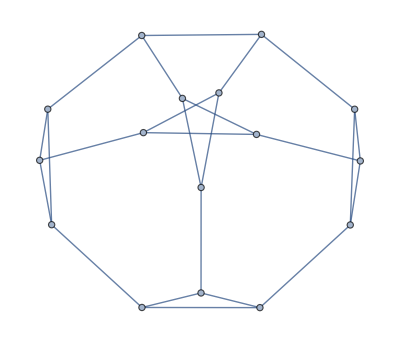
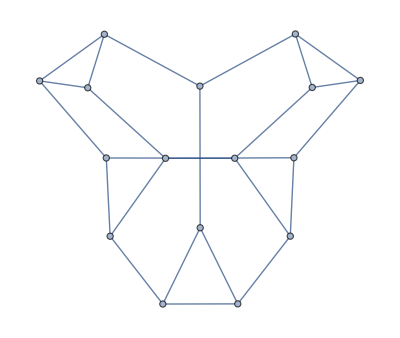
{3138,3576}-Graphics--Graphics-

```mathematica
For[i=1,i≤Length[CPair],i++,
G=GList[[CPair[[i,1]]]];
H=GList[[CPair[[i,2]]]];
If[HamiltonianGraphQ[G]&&HamiltonianGraphQ[H],Continue[];];
LG=LineGraph[G];
LH=LineGraph[H];
ChrPolyG=ChromaticPolynomial[LG,x];
ChrPolyH=ChromaticPolynomial[LH,x];
ChrIndG=If[(ChrPolyG/.{x->3})>0,3,4];
ChrIndH=If[(ChrPolyH/.{x->3})>0,3,4];
If[ChrIndG≠ChrIndH,Print[CPair[[i]],G,H]];
]
```

```mathematica
AdjG=AdjacencyMatrix[GList[[3576]]];
AdjH=AdjacencyMatrix[GList[[3138]]];
Print[Factor[CharacteristicPolynomial[AdjG,x]]];
Print[NullSpace[AdjG]];
Print[NullSpace[AdjH]];
```

(-3+x) x (2+x) (-2+x^2) (-3-x+x^2) (-2-4 x+x^3) (1-4 x+x^3) (-2-2 x+2 x^2+x^3)

{{0,-1,0,1,-1,0,0,0,1,1,-1,0,0,-1,0,1}}

{{2,1,-1,-1,1,0,0,-2,-1,0,2,-1,0,1,-2,1}}